# The Batmobile: Evolution’s Secret Weapon

There are two types of evolution. The first is what I call reactive. In reactive evolution, a random spread of organisms occurs, some organisms survive and some don’t. Over time, the organisms that are left are better at avoiding extinction. This type of evolution, where the environment makes the choices, is the only type of evolution most people are aware of. But there is a second type, and it is more important than the first type. The organisms that have been happily (or not so happily) putting their life in the hands of the environment, slowly find a way to take more control. Instead of producing a completely random spread of children, the organisms starts to develop mechanisms for predicting which children will fair better. These mechanisms are the eyes and ears of evolution. The steering wheel if you will. And in developing a steering wheel, the organisms go from being blind and drunk, stumbling through gene space, to being in the cockpit of an evolutionary Ferrari, carving through the environmental roads like “butta”, to steal a New Englandism. This may sound dramatic, but we will see that predictive evolution is really that much better.

Without understanding type 2 predictive evolution, many phenomenon in biology look very weird. I like to ask people the simple but difficult question: “Why do men exist?” If you imagine a female-only population, where each organism directly produces offspring, you would have twice the offspring, which would seemingly double your chances at survival, and double your chances at “finding” a more fit organism. And yet, the two-sex system, what biologists call “dioecy”, has evolved multiple times and been a stable feature of complex organisms for millions of years. So why is this?

Put simply, men are a tool for ranking genes, we are the testing ground for new genomic ideas, the R&D department of the population if you will. We are too busy doing are R&D duties to be bothered with reproducing ourselves. 

Stepping back for a second, I’ve been saying “organisms”, but predictive evolution works at all scales, going all the way down to the level of DNA. So in addition to answering the “man-question”, we will be able to explain meiosis, horizontal gene transfer, animal hierarchy, diploidism and show that all these are just instances of predictive evolution: mechanisms for exchanging and ranking potential successor genes. In doing this, we will understand evolution better than many biologists (like the buffoon Richard Dawkins) and we will debunk Stephen Wolfram’s ludicrous claim that sex is not essential to complex life. Even better, the prominence of predictive evolution is not restricted to the biological domain. In understanding it in biology, we will be able to easily make connections to adaptive processes outside of biology, like evolution of human culture, technological evolution and machine learning.

## The Road Model

```mathematica
SetOptions[EvaluationNotebook[],PageWidth->600]
```

Our road model has two dimensions. On the x-axis we have time and on the y-axis we have genotype. The size of the population is just the number of points on the y-axis at any given time. Each gene “lives” for some fixed time and then branches at some angle. The number of genes that “survive and reproduce” is limited by a maximum population size. For now, the genes who reproduce are chosen at random. This process repeats for a certain number of steps:

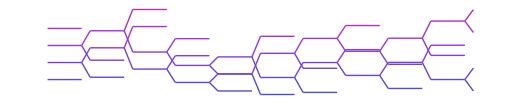

We can decrease the lifespan of each gene:

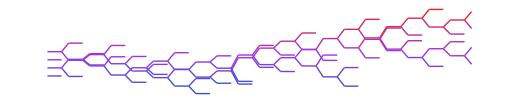

We can increase the size of the population:

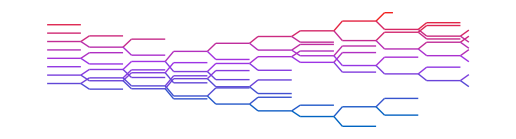

And we can increase the branching angle, i.e. the rate of change between generations:

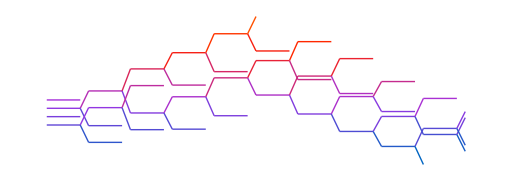

Now we add our environmental road. If an organism exits the road, it dies and does not reproduce. If the number of surviving parents exceeds the maximum population, then the reproducers are chosen at random:

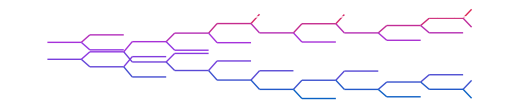

```mathematica
start = 5; 
width = 5;
lifetime = 4;
rad = 1;
var = 0.1;
roadlen = 50;
maxorgs = 4;
minwidth=5;
SeedRandom[63];
midroad = Table[{x, start}, {x, 1, roadlen}];
toproad =  {#[[1]], #[[2]]+ width}&/@ midroad; 
bottomroad =  {#[[1]], #[[2]]-width}&/@ midroad; 
hier = False;
inits = Table[{0, i}, {i,start,start + 2, 8/maxorgs}];
reaped =Reap[NestList[evolve, inits, Floor[roadlen/(lifetime+birth )]]];
evos = reaped[[1]];
lines = Line/@ reaped[[2, 1]];
toplines = Line/@ Partition[toproad, 2, 1];
bottomlines = Line/@ Partition[bottomroad, 2, 1]; 
styled = Style[#, blend[#[[1, 2, 2]] / 20]]&/@ lines;
Graphics[{styled,White,toplines, bottomlines}]
```

Increasing the population and the number of steps, we can get a feel for how different levels of variation and different lifetimes effect how the population moves through time:

### Longer sims

Base:

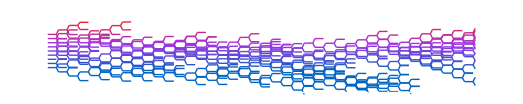

Shorter lifetime:

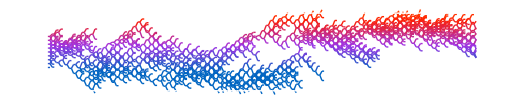

Longer lifetime

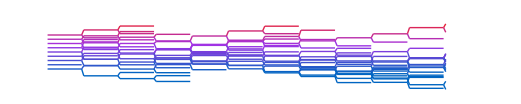

Higher variation

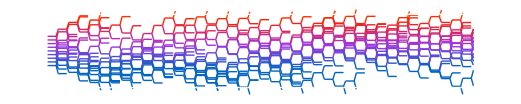

### Rest

At this scale the populations look more like a single entity. With a shorter lifetime, you can see the genes bounce around more. With a longer lifetime everything is very stable. With higher variation the population spreads out more. To use an analogy from physics, you could think of the population size as the mass, the lifetime as the temperature, and the variation as the attraction between particles. In this sense, low variation and longer lifetime populations behave more like fluids, while high variation and shorter lifetimes behave more like gases.

Now let’s add to our model of the environment. We will use bends in the road represent changes in the environment:

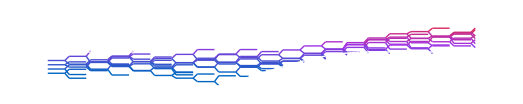

A more volatile environment incentivizes more gene variation, in the first case we have mild variation between generations and aren’t able to make the turn. In the second case we increase the variation and survive:

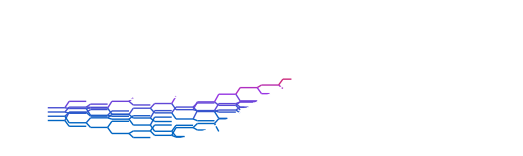

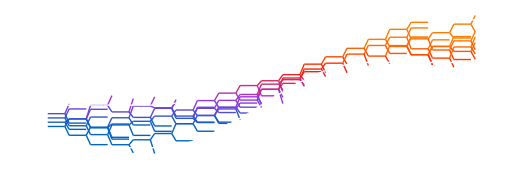

Going further we see the same effect:

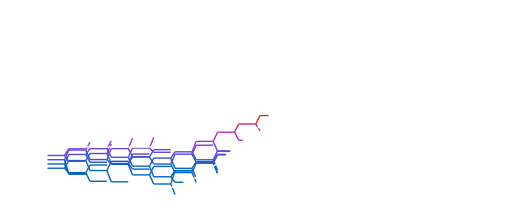

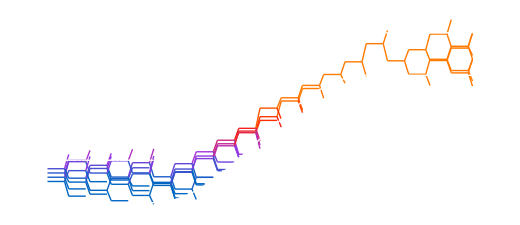

The width of the road represents the size of the “fitness-space”. When the road is narrow, small variations between generations are incentivized:

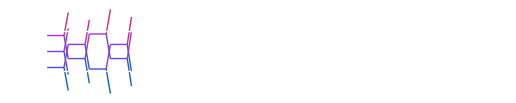

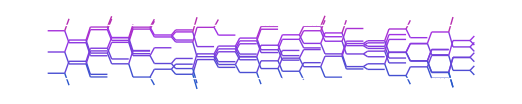

Because of this dichotomy between road width and road volatility, its interesting to look at the ratio between the turn angle and the width of the road. There is some point in this ratio where life can no longer evolve. If we set our max population

Variation = 1: Can’t turn.

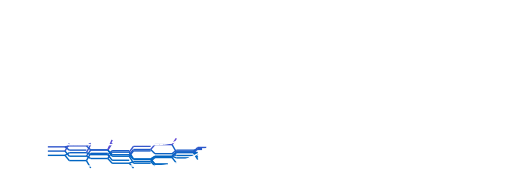

Variation = 2: Does better but still can’t turn.

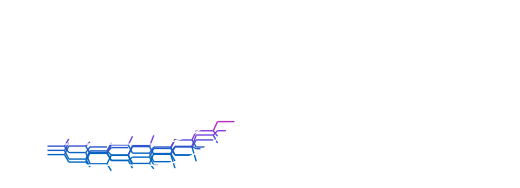

Variation = 3: Gets further but still can’t turn.

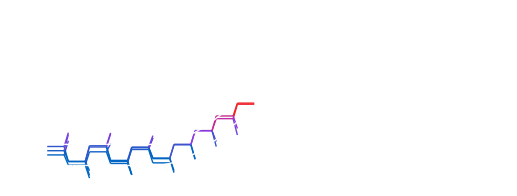

Variation 4: Can’t navigate the width:

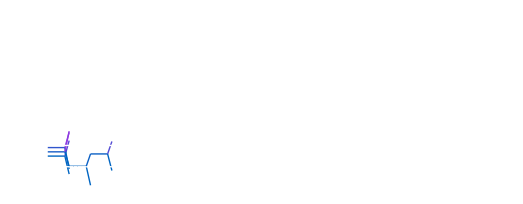

This road represents an environment in which life will not evolve.

This problem, of dealing with narrow and winding roads is particularly acute for complex organisms, who tend to have smaller populations and slower reproduction rates due to their larger size.

We can see how a larger population navigates volatility better:

Similarly, shorter lifetimes also do better with volatility:

Lifetime 4:

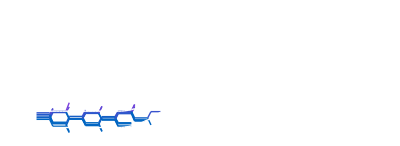

Lifetime 3:

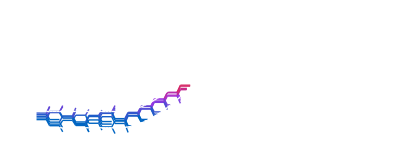

Lifetime 2:

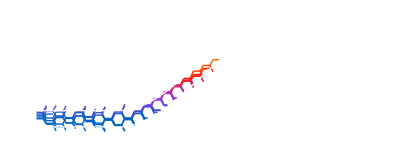

Lifetime 1:

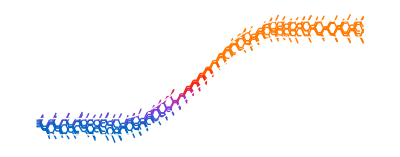

So what do complex organisms do? This is where predictive evolution comes in. Up until this point, we’ve only been looking at reactive evolution. Meaning, the selection process is entirely determined by the environment. In this paradigm, the population “crashes” into the walls of the road, with the genes that avoided the crash surviving. 

Over time though, a better mechanism evolves. The genes figure out ways to rank themselves according to their fitness. In our case, fitness is simply the distance from the edge of either side of the road. To see the power of self-ranking we will imagine a similar environment to the one above, this time with a bottleneck instead of a turn. Starting from the bottom, here is our reactive population evolving towards

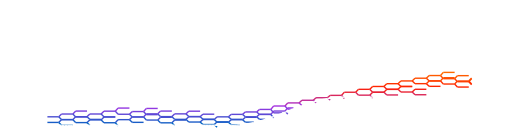

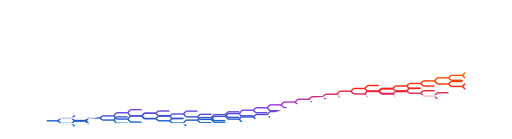

with a narrow starting section followed by a turn and another bottleneck:

Our complex reactively evolving population struggles in this terrain:

But, instead of choosing randomly who reproduces, we can select organisms to reproduce in order of their distance from the edge of the road, like so:

This procedure allows our small population to steer itself past the bottleneck:

The most obvious example of this mechanism in biology is animal hierarchy. The males have different, sometimes ingenious ways of ranking themselves. To use a favorite of the biologist John Maynard Smith, two rival male spiders will bounce on their webs like a trampoline. The one that bounces higher is deemed lighter and therefore loses the battle. This is often seen as simply a game-theoretic mechanism for resolving conflict. Instead of fighting, both spiders would rather use an approximation for the fight. While there is truth to this, there is more to these simulations than conflict resolution. Namely, they are also fitness simulations. If the battle between the spiders was just conflict resolution, you may wonder, “Why don’t they just keep evolving to be larger?”. Well, the difference in mass actually just corresponds to each spider’s hydration level (these are desert spiders by the way), not their physical size. So you could be a smaller but smarter spider, find more water, and win the battle. 

This is a simple but radical idea. This trampoline duel is not just a selfish way for two males to split resources. It is beneficial for all the other spiders. The females can now easily tell who is the fitter spider. The fittest male will then be matched with the fittest female. This will give the fittest genes the highest probability of being passed on. In the long-run, the population benefits. 

Extending this concept to human societies, the rules are related but slightly different. For whatever reason (maybe language), human males can team up more effectively than most animal males. Because of this, a weak male with a lot of friends can defeat a strong loner. So the tests are more just about how many friends you have. But again, this popularity contest is not just conflict resolution. In being popular, you are also likely to be more fit. Gaining friends requires competence, you’re probably smart, funny (which is just a form of intelligence), skilled, or tough. So the highest status females go for the highest status males. Just like with the spiders, this is beneficial for the population in the long-run. 

What I’m getting at here is this radical and somewhat taboo notion that the highest status humans are the best humans. This should of course be taken with a grain of salt. The ranking system is a very noisy metric for competence, especially in the modern volatile post-alphabet world. Regardless, while a noisy metric of competence, status is still a metric. Our culture actively tries to avoid this idea, the U.S. was, in some ways founded on its denial, “All men are created equal”. But I actually think that seeing the hierachy as the steering wheel that it is, is an optimistic view. 

Jordan Peterson points out the ubiquity of the hierachy in his book 12 Rules for Life. But his perspective left a bad taste in my mouth. He does not try to explain the hierarchy, instead just encouraging readers to accept its existence and go on competing for the biggest slice of pie. But, without seeing that the hierachy is a steering mechanism, it’s easy to fall into the depressing Malthusian trap of thinking that the pie is fixed. In my view though, in playing the status game, you are simply doing your part in pointing civilization in the right direction. And there is no limit to the size of the pie humans can create in the future. So my philosophy, is to play the status game, let the better man win, and be happy that the group is better off because of it.

Getting back to our model, so far, we’ve explicitly selected the genes furthest from death. But in practice, this process is much less black and white. A more accurate procedure would be to do some mixing, with the successor genes being pulled in the direction of the most fit predecessors. We can think about this as a high-level model for phenomena like diploidism, horizontal gene transfer and meiosis.

Adjusting the direction of our branches towards the most central (fittest) genes we get:

This also allows our population to steer past the bottleneck:

Combining these two procedures we get even better results:

## Functions

```mathematica
isalive[{x_, y_}]:= If[y > bottomroad[[x+1, 2]] && y < toproad[[x+1, 2]], True, False]
(*isalive[{x_, y_}]:= If[y > midroad[[x+1, 2]]+ widthfunc[x+1] && y < midroad[[x+1, 2]]- widthfunc[x+1], True, False]*)
getdeath[{x_, y_}]:= Block[{i = x, j = y},
If[y == -Infinity, Sow[{{x, y}, {x+lifetime, -Infinity}}], {x+lifetime, -Infinity}];
While[i < x + lifetime&&isalive[{i, j}], i++];
Sow[{{x, y}, {i, j}}];
{i, j}]
reproduce[parents_]:= Block[{alive,numrep, torep,rand, lines, children}, 
alive =Select[parents, isalive];
If[alive != {},
rank = SortBy[alive, Abs[#[[2]] - midroad[[#[[1]]+1, 2]]]&];
numrep = Floor[maxorgs/ 2];
torep =If[hier == True, Take[rank, UpTo[numrep]], RandomSample[alive, UpTo[numrep]]];
(*best = MinimalBy[torep, Abs[#[[2]] - midroad[[#[[1]]+1, 2]]]&][[1]];
pulled = If[best[[2]]>#[[2]], Min[best[[2]], #[[2]]+att],Max[best[[2]], #[[2]]-att]]&/@ torep;*)
rand = RandomVariate[NormalDistribution[rad, var]];
(*lines = MapThread[{Sow[{#,{#[[1]]+1, #2+rand }}],  Sow[{#, {#[[1]]+1, #2-rand}}]}&, {torep, pulled}];*)
lines = Map[{Sow[{#,{#[[1]]+birth, #[[2]]+rand }}],  Sow[{#, {#[[1]]+birth, #[[2]]-rand}}]}&, torep];
children =Flatten[lines, 1][[All, 2]], 
{}]

]
evolve[orgs_]:= Block[{parents = getdeath/@orgs}, reproduce[parents]]
blend[val_]:=Blend[RGBColor/@{Hue[0.58, 1., 0.76],Hue[0.77, 0.78, 0.9],Hue[0.02, 1., 1.],Hue[0.08, 1., 1.]},val]
```